## Problem 9

```mathematica
ClearAll["Global`*"];
(*Here I define the signal as a dynamic function*)
f[x_,k_,σ_]:=Sin[k*x]*Exp[-((x-0)^2/(2 σ^2))];
```

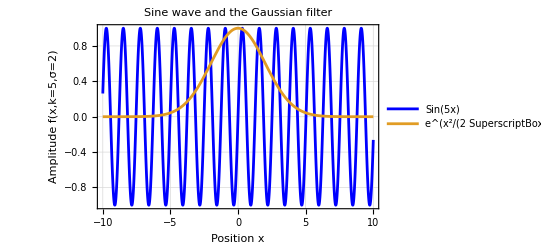

```mathematica
(*Here is how the sine and the Gaussian filter looks like separately*)Plot[{Sin[5*x],Exp[-((x-0)^2/(2 2^2))]},{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},FrameLabel->{"Position x","Amplitude f(x,k=5,σ=2)"},PlotLabel->"Sine wave and the Gaussian filter",PlotLegends->{"Sin(5x)","e^(x^2/(2 SuperscriptBox[σ, 2]))"},ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]
```

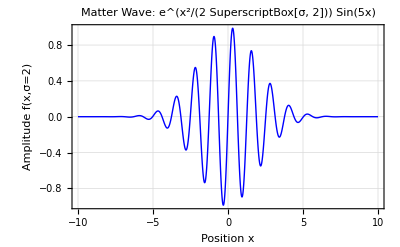

```mathematica
(*Here is how the function e^(x^2/(2 σ^2)) Sin(5x)looks like*)Plot[f[x,5,2],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},FrameLabel->{"Position x","Amplitude f(x,σ=2)"},PlotLabel->"Matter Wave: e^(x^2/(2 SuperscriptBox[σ, 2])) Sin(5x)",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]
```

### Problem 9 - Part 1 (Effect of the wave number k)

```mathematica
(*PART 9 of ASSINGMENT2:*)
(*I use Manipulate command to visually see how the function changes for different values of the wave number k and σ*)Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
```

As we can see from the plot, the number of the wave included in the plot increases as the wave number k increases. This is because the wave number k represents the frequency of the sine wave signal. As the frequency increases, more cycles will be included in a certain time period.

### Problem 9 - Part 2 (Effect of the standard deviation σ of Gaussian)

```mathematica
Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
Manipulate[Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"Position","Amplitude"},PlotLabel->"Sine Wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],{{k,1,"Wave Number k"},0.1,5,0.1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.1}]
```

As we can see from the plot, the range of the sine wave signal with non-zero values increases as the standard deviation σ of Gaussian increases. Since the signal is the standard sine wave multiplied by the Gaussian function, the Gaussian filter can be regarded as the proportion of the signal that is allowed to pass the filter. The increase of the standard deviation σ means the Gaussian is distributed in a larger range. This allows the signal from a larger range of input to pass.

## Problem 10

```mathematica
(*Then I obtain the Fourier Coefficients, its magnitude and Phase as a dynamic function*)
FourierCoeff[freqValue_,k_,σ_]:=NIntegrate[f[x,k,σ]Exp[-I 2 Pi freqValue x],{x,-10,10}];
FourierCoeffMag[freqValue_,k_,σ_]:=Abs[FourierCoeff[freqValue,k,σ]];
FourierCoeffPhase[freqValue_,k_,σ_]:=Arg[FourierCoeff[freqValue,k,σ]];
```

### Problem 10 - Part 1 (Effect of the wave number k)

```mathematica
(*PART 10 of ASSINGMENT2:*)
(*You can now manipulate the energy density spectrum by changing k and σ *)Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
```

As we can see from the plot, the peak of the energy density spectrum moves to a higher frequency value as the wave number k increases. This is because the energy density spectrum shows the contribution of the signal with different frequency and the wave number k represents the frequency of the sine wave signal. With a higher frequency of the signal, the peak amplitude moves further away from the origin.

### Problem 10 - Part 2 (Effect of the standard deviation σ of Gaussian)

```mathematica
Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
Manipulate[Column[{Plot[f[x,k,σ],{x,-10,10},PlotRange->All,PlotStyle->{Blue},FrameLabel->{"Position x","Amplitude f(x)"},PlotLabel->"Sine wave with Gaussian Envelope",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All],Plot[Abs[FourierCoeffMag[freqValue,k,σ]]^2,{freqValue,-1,1},PlotRange->All,PlotStyle->{Red},FrameLabel->{"Frequency 𝒻 (in Hz)","|F(𝒻)|^2"},PlotLabel->"Energy density spectrum",ImageSize->400,LabelStyle->{RGBColor[0,0,0],FontSize->12,FontFamily->"Times"},GridLines-> Automatic,Frame-> True,PlotRange->All]}],{{k,1,"Wave Number k"},1,5,1},{{σ,1,"Standard Deviation of Gaussian σ"},0.5,2,0.5}]
```

In this case the wave number k is fixed, which means the frequency of the signal remains constant. So the frequency corresponding to the peak amplitude of the energy density spectrum is the same for all the 3 cases. The increase of the standard deviation σ means the Gaussian is distributed in a larger range. This allows the signal from a larger range of input to pass and results in more total energy being included in the signal. So the peak value of the energy density spectrum increases with the increase of the standard deviation σ.